```mathematica
W=110;
θ=π/90;
kd=θ;
ϕ=(2*π)/3;
l=0.5;
m=3;
n=2;
y=kd*l^2;
Δ=(√3)/2*y;
k1=y/l^2;
k2=(2*π)/Δ;
v=120;
s=30;
```

Eigenvalues::arh: Because finding 120 out of the 120 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues :: arh will be suppressed during this calculation.

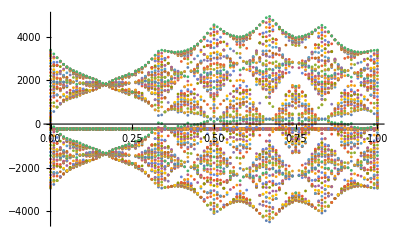

```mathematica
H[θ_]:=v √(n+1)*Exp[-ⅈ*θ]
h[θ_]:=v √(m+1)*Exp[-ⅈ*θ]
Td[α_,j_]:=√(Factorial[m]/Factorial[n])(-ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[-ⅈ*kd*y]Exp[-4π*ⅈ*α*j]
td[α_,j_]:=√(Factorial[m]/Factorial[n])(+ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[+ⅈ*kd*y]Exp[+4π*ⅈ*α*j];
Tn[α_,j_]:=√(Factorial[m]/Factorial[n])(√3(kd*l)/2+ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[ⅈ*k2*Δ]Exp[ⅈ*(kd*y)/2]Exp[π*ⅈ*α(2j-1)];
tn[α_,j_]:=√(Factorial[m]/Factorial[n])(√3(kd*l)/2-ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[-ⅈ*k2*Δ]Exp[-ⅈ*(kd*y)/2]Exp[-π*ⅈ*α(2j-1)];
Ud[α_,j_]:=√(Factorial[m]/Factorial[n])(-√3(kd*l)/2+ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[-ⅈ*k2*Δ]Exp[ⅈ*(kd*y)/2]Exp[π*ⅈ*α(2j+1)];
un[α_,j_]:=√(Factorial[m]/Factorial[n])(-√3(kd*l)/2-ⅈ*((kd*l)/2))^(n-m)Exp[-(kd*l)^2/2]LaguerreL[m,Abs[n-m],((kd*l)/(√2))^2]Exp[ⅈ*k2*Δ]Exp[-ⅈ*(kd*y)/2]Exp[-π*ⅈ*α(2j+1)];
Du1[α_]:=Delete[Flatten[Table[{H[θ],Td[α,j],h[-θ],tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ]},{j,0,s-1}]],4*s];
Du2[α_]:=Delete[Flatten[Table[{Td[α,j],Td[α,j],tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ]},{j,0,s-1}]],{{4*s},{4*s-1}}];
Du3[α_]:=Delete[Flatten[Table[{Td[α,j],0,tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2}}];
Du5[α_]:=Delete[Flatten[Table[{0,Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4}}];
Du6[α_]:=Delete[Flatten[Table[{Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4},{4*s-5}}];
Du7[α_]:=Delete[Flatten[Table[{Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],0,0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4},{4*s-5},{4*s-6}}];
du1[α_]:=Delete[Flatten[Table[{H[-θ],td[α,j],h[θ],Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ]},{j,0,s-1}]],4*s];
du2[α_]:=Delete[Flatten[Table[{td[α,j],td[α,j],Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ]},{j,0,s-1}]],{{4*s},{4*s-1}}];
du3[α_]:=Delete[Flatten[Table[{td[α,j],0,Tn[α,j+1]*Exp[-ⅈ*ϕ]+Ud[α,j+1]*Exp[ⅈ*ϕ],0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2}}];
du5[α_]:=Delete[Flatten[Table[{0,tn[α,j+1]*Exp[+ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4}}];
du6[α_]:=Delete[Flatten[Table[{tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4},{4*s-5}}];
du7[α_]:=Delete[Flatten[Table[{tn[α,j+1]*Exp[ⅈ*ϕ]+un[α,j+1]*Exp[-ⅈ*ϕ],0,0,0},{j,0,s-1}]],{{4*s},{4*s-1},{4*s-2},{4*s-3},{4*s-4},{4*s-5},{4*s-6}}];
b[α_]:=SparseArray[{Band[{1,2},{4*s,4*s}]->Du1[α],Band[{1,3},{4*s,4*s}]->Du2[α],Band[{1,4},{4*s,4*s}]->Du3[α],Band[{1,6},{4*s,4*s}]->Du5[α],Band[{1,7},{4*s,4*s}]->Du6[α],Band[{1,8},{4*s,4*s}]->Du7[α],Band[{2,1},{4*s,4*s}]->du1[α],Band[{3,1},{4*s,4*s}]->du2[α],Band[{4,1},{4*s,4*s}]->du3[α],Band[{6,1},{4*s,4*s}]->du5[α],Band[{7,1},{4*s,4*s}]->du6[α],Band[{8,1},{4*s,4*s}]->du7[α]},{4*s,4*s}];
Block[{getEv},getEv[α_?NumericQ]:=getEv[α]=Sort@Eigenvalues[b[α]];
getEv[α_?NumericQ,n1_]:=getEv[α][[n1]];
DiscretePlot[Evaluate@Table[getEv[α,n1],{n1,4*s}],{α,0,1,0.01},Filling->None,Joined->False,PlotStyle->PointSize[0.005]]]
```

```mathematica
Block[{getEv},getEv[α_?NumericQ]:=getEv[α]=Sort@Eigenvalues[b[α]];
getEv[α_?NumericQ,n1_]:=getEv[α][[n1]];
DiscretePlot[Evaluate@Table[getEv[α,n1],{n1,4*s}],{α,0,1,0.01},Filling->None,Joined->False,PlotStyle->PointSize[0.005]]]
```

```mathematica
Eigenvalues[b[0.5]]
```

{3755.,-3307.44,1811.12,-1363.57,580.946,-240.214,-239.851,-239.84,-208.115,-207.718,-207.709,-132.618}

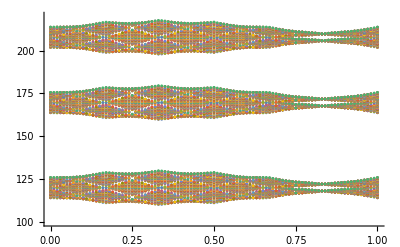

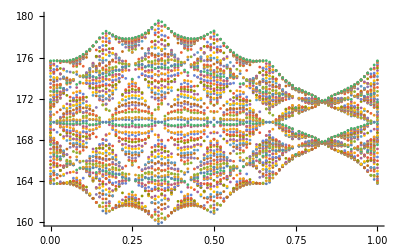

```mathematica
Show[%38,%37,%36,PlotRange->{{0,1},{100,220}}]
Show[%38,%37,%36,PlotRange->{{0,1},{160,180}}]
```